```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

## Direct basis

```mathematica
p[l_,α_]:=N[l α+(1-α) IntegerPart[l/(1+α)]];
```

```mathematica
τ=N [(1+Sqrt[5])/2];
t[i_]:=p[i+1,1/τ]-p[i,1/τ]
```

```mathematica
t[5]
```

0.618034

```mathematica
(* rk: t[i] is related to IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #] *)
(IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #])&/@Range[0,4]
(IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #]-t[#])&/@Range[20]//Chop
```

{0,1,0,1,1}

{0,-0.618034,0,0,-0.618034,0,-0.618034,0,0,-0.618034,0,0,-0.618034,0,-0.618034,0,0,-0.618034,0,-0.618034}

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar,Fn},
Fn=Fibonacci[n];
tbl=Table[{i,i+1}->t[i],{i,1,Fn-1}];
ar=SparseArray[tbl,{Fn,Fn}];
Normal[ar+Transpose[ar]]
]
h[6]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0.618034 | 0 | 0 | 0 | 0 | 0
0 | 0.618034 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0.618034 | 0 | 0
0 | 0 | 0 | 0 | 0.618034 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.618034
0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | 0)

```mathematica
(* hamiltonien avec conditions aux bords périodiques *)
Clear[hp];
hp[n_]:=Block[{tbl,ar,Fn},
Fn=Fibonacci[n];
tbl=Table[{i,i+1}->t[i],{i,1,Fn-1}];
AppendTo[tbl,{1,Fn}->t[Fn-1]];
ar=SparseArray[tbl,{Fn,Fn}];
Normal[ar+Transpose[ar]]
]
hp[6]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0.618034
1. | 0 | 0.618034 | 0 | 0 | 0 | 0 | 0
0 | 0.618034 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0.618034 | 0 | 0
0 | 0 | 0 | 0 | 0.618034 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.618034
0.618034 | 0 | 0 | 0 | 0 | 0 | 0.618034 | 0)

```mathematica
Dimensions[%50]
```

{1}

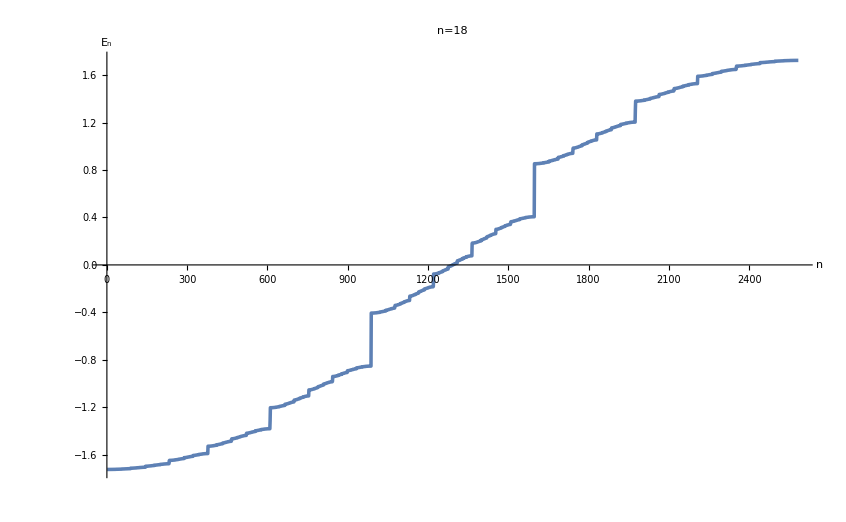

```mathematica
(* spectre *)
vp1=Block[{vp,plot,i=18},
vp=Sort[Eigenvalues[hp[i]]];
plot=ListPlot[vp,Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"n="<>ToString[i],PlotStyle->Thickness[th]];
Export[dir<>"/data/spectrum_fibo_chain.png",plot];
Print[plot];
vp
];
```

## Co-numbered basis

### Hamiltonian written in the normal basis

```mathematica
τ=N [(1+Sqrt[5])/2];
ϕ=N[1+√2];
rot=28;
fib[n_]:=IntegerPart[τ^-1( n+1+rot)]-IntegerPart[τ^-1 (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];
```

```mathematica
Clear[h];
h[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
(* periodic boundary conditions *)
(*AppendTo[tbl,{1,F2}->tw];*)
(* potential *)
AppendTo[tbl,{40,40}->10.];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
h[5,tw,ts]//MatrixForm
```

(20. | ts | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ts | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | tw | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | tw | 0 | ts | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ts | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | tw | 0 | tw | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | tw | 0 | ts | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ts | 0 | tw | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | ts | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ts | 0 | tw | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | tw | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | tw | 0 | ts
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ts | 0)

```mathematica
(* wavefunctions by co-label and by IDoS *)
wf=Block[{val,vec,i=9,ts=1.,tw=1./10.},
{val,vec}=Eigensystem[h[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

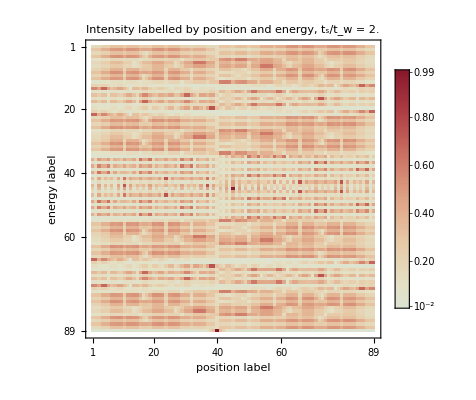

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","position label"},PlotLabel->"Intensity labelled by position and energy, t_s/t_w = 2.",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
(*Export[dir<>"/data/cobasis_idos.png",%,ImageSize->600]*)
```

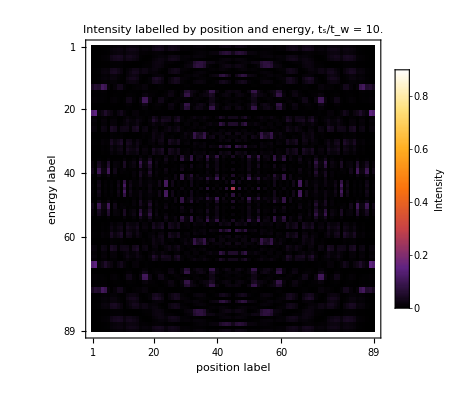

```mathematica
r={0,0.9};
color="SunsetColors";
p=MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","position label"},PlotLabel->"Intensity labelled by position and energy, t_s/t_w = 10.",ColorFunctionScaling->False,ColorFunction->(ColorData[color,Rescale[#,r,{0,1}]]&)];
bl=BarLegend[{color,r},LegendLabel->"Intensity"];
Legended[p,bl]
(*Export[dir<>"/data/basis_idos.png",%,ImageSize->600]*)
```

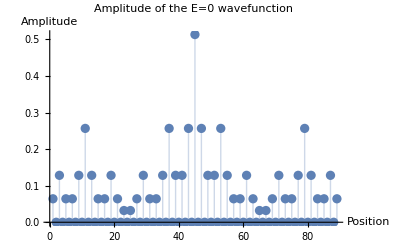

/home/nicolas/git/spectrum_quasicrystals/Fibonacci//data/amplitude_wf.pdf

```mathematica
ListPlot[Abs[wf[[45]]],PlotRange->All,Filling->Axis,PlotRange->All,PlotLabel->"Amplitude of the E=0 wavefunction",AxesLabel->{"Position","Amplitude"}]
Export[dir<>"/data/amplitude_wf.pdf",%]
```

### Hamiltonian directly written in the co basis

```mathematica
hco[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
hco[5,tw,ts]//MatrixForm;
```

```mathematica
Block[{vp,i=16,ts=1.,tw=.3,plot},
vp=Sort[Eigenvalues[hco[i,tw,ts]]];
plot=ListPlot[vp,Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"n="<>ToString[i],PlotStyle->Thickness[th]];
(*Print[plot];*)
]
```

```mathematica
(* wavefunctions by co-label and by IDoS *)
wf=Block[{val,vec,i=9,ts=1.,tw=1./10.},
{val,vec}=Eigensystem[hco[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

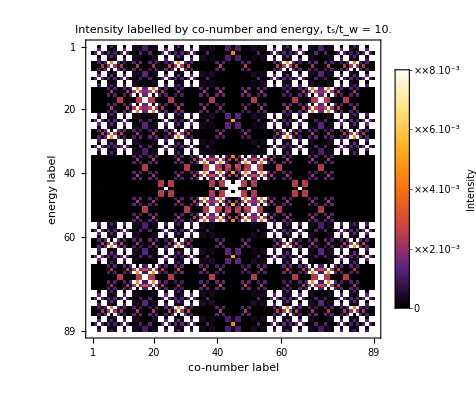

StringJoin::string: String expected at position 1 in dir <> "data/test.png".

Export::chtype: First argument dir <> "data/test.png" is not a valid file specification.

$Failed

```mathematica
r={0,0.008};
color="SunsetColors";
p=MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","co-number label"},PlotLabel->"Intensity labelled by co-number and energy, t_s/t_w = 10.",ColorFunctionScaling->False,ColorFunction->(ColorData[color,Rescale[#,r,{0,1}]]&),ImageSize->400];
bl=BarLegend[{color,r},LegendLabel->"Intensity"];
Legended[p,bl]
Export[dir<>"data/test.png",%,ImageResolution->400]
```

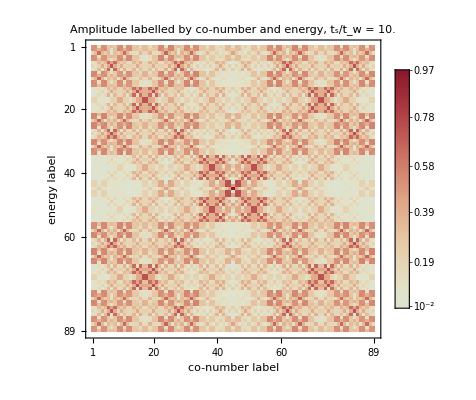

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/test.png

```mathematica
MatrixPlot [Abs[wf],FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy, t_s/t_w = 10.",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
Export[dir<>"data/test.png",%,ImageResolution->150,ImageSize->2000]
(*Export[dir<>"/data/cobasis_idos.png",%,ImageSize->600]*)
```

```mathematica
ColorData["VisibleSpectrum"]
```

```mathematica
(* adding a potential V at the site Subscript[F, n+1] of the Subscript[F, n+2] chain *)
hco[n_,tw_,ts_,V_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
AppendTo[tbls,{F0,F0}->V/2];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* wavefunctions by co-label and by IDoS *)
wf=Block[{val,vec,i=8,ts=1.,tw=1./10.,V=10.},
{val,vec}=Eigensystem[hco[i,tw,ts,V]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

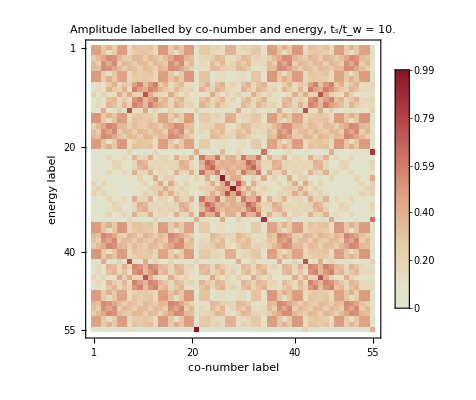

```mathematica
MatrixPlot [Abs[wf]^2,FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy, t_s/t_w = 10.",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
(*Export[dir<>"/data/cobasis_idos.png",%,ImageSize->600]*)
```

#### Pass to the bonding-antibonding basis

Passing to the bonding-antibonding basis at step n “diagonalizes” the Hamiltonian at step n into three diagonal blocks: bonding molecules, atoms and antibonding molecules.

```mathematica
(* matrix changin basis *)
pass[n_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],bond,at,anti},
bond=Table[{{i,i}->1,{i,i+F1}->1},{i,F0}]//Flatten;
bond=2^(-1/2)SparseArray[bond,{F2,F2}]//Normal;
at=Table[{i+F0,i+F0}->1,{i,F1-F0}]//Flatten;
at=SparseArray[at,{F2,F2}]//Normal;
anti=Table[{{i+F1,i}->1,{i+F1,i+F1}->-1},{i,F0}]//Flatten;
anti=2^(-1/2)SparseArray[anti,{F2,F2}]//Normal;

bond+at+anti
]
```

```mathematica
n=5;
hco[n,ρ,1]//MatrixForm
Transpose[pass[n]].hco[n,ρ,1].pass[n]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | ρ | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ρ | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ρ | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ρ | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ρ | 0 | 0 | 1
ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ρ | 0 | 0
0 | ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ρ | 0
0 | 0 | ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ρ
1 | 0 | 0 | ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | ρ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | ρ | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | ρ/2 | 0 | ρ/(√2) | 0 | 0 | 0 | 0 | 0 | ρ/2 | 0
0 | 1 | 0 | 0 | ρ/2 | 0 | ρ/(√2) | 0 | 0 | 0 | 0 | 0 | ρ/2
0 | 0 | 1 | 0 | 0 | ρ/(√2) | 0 | ρ/(√2) | 0 | 0 | 0 | 0 | 0
ρ/2 | 0 | 0 | 1 | 0 | 0 | ρ/(√2) | 0 | -ρ/2 | 0 | 0 | 0 | 0
0 | ρ/2 | 0 | 0 | 1 | 0 | 0 | ρ/(√2) | 0 | -ρ/2 | 0 | 0 | 0
ρ/(√2) | 0 | ρ/(√2) | 0 | 0 | 0 | 0 | 0 | ρ/(√2) | 0 | -ρ/(√2) | 0 | 0
0 | ρ/(√2) | 0 | ρ/(√2) | 0 | 0 | 0 | 0 | 0 | ρ/(√2) | 0 | -ρ/(√2) | 0
0 | 0 | ρ/(√2) | 0 | ρ/(√2) | 0 | 0 | 0 | 0 | 0 | ρ/(√2) | 0 | -ρ/(√2)
0 | 0 | 0 | -ρ/2 | 0 | ρ/(√2) | 0 | 0 | -1 | 0 | 0 | -ρ/2 | 0
0 | 0 | 0 | 0 | -ρ/2 | 0 | ρ/(√2) | 0 | 0 | -1 | 0 | 0 | -ρ/2
0 | 0 | 0 | 0 | 0 | -ρ/(√2) | 0 | ρ/(√2) | 0 | 0 | -1 | 0 | 0
ρ/2 | 0 | 0 | 0 | 0 | 0 | -ρ/(√2) | 0 | -ρ/2 | 0 | 0 | -1 | 0
0 | ρ/2 | 0 | 0 | 0 | 0 | 0 | -ρ/(√2) | 0 | -ρ/2 | 0 | 0 | -1)

```mathematica
(* wavefunctions by co-label and by IDoS *)
wf=Block[{val,vec,i=9,ts=1.,tw=1./10.,p},
p=pass[i];
{val,vec}=Eigensystem[Transpose[p].hco[i,tw,ts].p];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

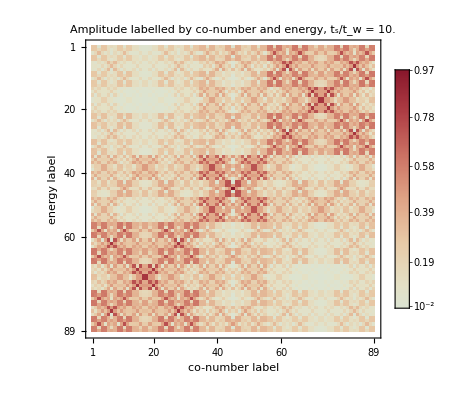

```mathematica
MatrixPlot [Abs[wf],FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy, t_s/t_w = 10.",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
(*Export[dir<>"data/test.png",%,ImageResolution->150,ImageSize->2000]*)
```

#### Weak quasiperidicity limit

```mathematica
(* periodic wf *)
Clear[n];
n=10;
wfp=Block[{val,vec,i=n,ts=1.,tw=1.},
{val,vec}=Eigensystem[hco[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
(* weakly quasiperiodic wf *)
ϵ=0.01;
wfqp=Block[{val,vec,i=n,ts=1.,tw=1.-ϵ},
{val,vec}=Eigensystem[hco[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

```mathematica
(* let's plot the two!*)
MatrixPlot [wfp,FrameLabel->{"integrated density of states","co-numbered position"},PlotLabel->"WF coefficients ordered by co-number and energy",ColorFunction->"ThermometerColors"];
MatrixPlot [wfqp,FrameLabel->{"integrated density of states","co-numbered position"},PlotLabel->"WF coefficients ordered by co-number and energy",ColorFunction->"ThermometerColors"];
(* let's plot the difference!*)
MatrixPlot [wfp-wfqp,FrameLabel->{"integrated density of states","co-numbered position"},PlotLabel->"WF coefficients ordered by co-number and energy",ColorFunction->"ThermometerColors"];
```